## Definitions and setup

```mathematica
wd =SetDirectory@NotebookDirectory[];
```

```mathematica
states = {"Υ(1S)","Υ(2S)","χ_b(1P)","Υ(3S)","χ_b(2P)","Υ_2(1D)"};
tickSpecification=Table[{i,states[[i]]},{i,1,6}];
```

```mathematica
mapPoint[x_] := Around[x[[1]],x[[2]]]
```

```mathematica
ImportData[dir_]:=Module[{mean,stderr},
Clear[data];
data=Import[wd<>"/../"<>dir<>"/ratios.tsv"];
Print["Processing ",Length[data]," trajectories"];
mean=Mean[data];
stderr=StandardDeviation[data]/Sqrt[Length[data]];
mapPoint/@Transpose[{mean,stderr}]
]
```

## Plot setup

```mathematica
SetOptions[Plot,Frame->True,Axes->False,ImageSize->500,AspectRatio->0.75,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
SetOptions[ListPlot,Frame->True,Axes->False,ImageSize->500,AspectRatio->0.75,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
```

## Peek at the data

```mathematica
raaData=ImportData["output"]
```

Processing 3 trajectories

{1,1,0,1,0,0,0,0}

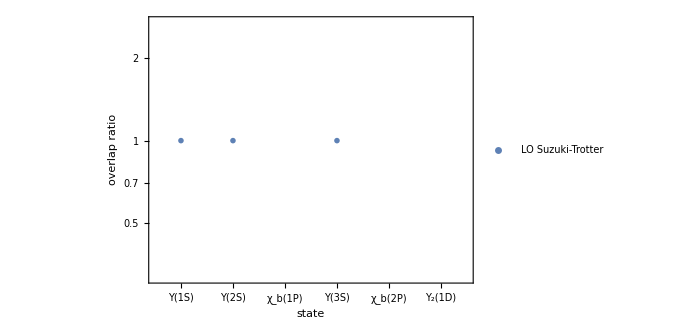

```mathematica
ListLogPlot[{raaData},ImageSize->500,PlotMarkers->{"OpenMarkers",7},Frame->True,FrameStyle->AbsoluteThickness[1],BaseStyle->16,AspectRatio->0.67,FrameLabel->{"state","overlap ratio"},PlotRange->{{0.5,6.5},All(*{0,1}*)},FrameTicks->{{Automatic,Automatic},{tickSpecification,Automatic}},PlotLegends->Placed[LineLegend[{"LO Suzuki-Trotter","LO Crank-Nicholson","NLO Crank-Nicholson"},LegendMargins->10, LabelStyle->Directive[FontSize->14]],{Right,Top}]]
```

```mathematica
myData={{{1,raaData0[[1]]}},{{1,raaData1[[1]]}},{{1,raaData2[[1]]}}}
ListPlot[myData,ImageSize->500,PlotMarkers->{"OpenMarkers",7},Frame->True,FrameStyle->AbsoluteThickness[1],BaseStyle->16,AspectRatio->0.67,FrameLabel->{"state","overlap ratio"},PlotRange->{{0.5,1.5},All},FrameTicks->{{Automatic,Automatic},{tickSpecification,Automatic}},PlotLegends->Placed[LineLegend[{"LO Suzuki-Trotter","LO Crank-Nicholson","NLO Crank-Nicholson"},LegendMargins->20, LabelStyle->Directive[FontSize->14]],{Left,Top}]]
```

Part::partd: Part specification raaData0⟦1⟧ is longer than depth of object.

Part::partd: Part specification raaData1⟦1⟧ is longer than depth of object.

Part::partd: Part specification raaData2⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{{1,raaData0⟦1⟧}},{{1,raaData1⟦1⟧}},{{1,raaData2⟦1⟧}}}

-Graphics-

## Peek at the data

```mathematica
raaData0=ImportData["1s/osc-0"]
raaData1=ImportData["1s/osc-1"]
raaData2=ImportData["1s/osc-2"]
```

Import::nffil: File /home/sawin/Desktop/QuarkoniaInQGP/qtraj-nlo/mathematica/../1s/osc-0/ratios.tsv not found during Import.

Processing 0 trajectories

Power::infy: Infinite expression 1/0 encountered.

Part::partw: Part 2 of Mean[$Failed] does not exist.

Part::partw: Part 1 of ComplexInfinity does not exist.

Part::partw: Part 2 of ComplexInfinity does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{$FailedMean[$Failed]⟦2⟧,ComplexInfinity⟦1⟧ComplexInfinity⟦2⟧}

Import::nffil: File /home/sawin/Desktop/QuarkoniaInQGP/qtraj-nlo/mathematica/../1s/osc-1/ratios.tsv not found during Import.

Processing 0 trajectories

Power::infy: Infinite expression 1/0 encountered.

Part::partw: Part 2 of Mean[$Failed] does not exist.

Part::partw: Part 1 of ComplexInfinity does not exist.

Part::partw: Part 2 of ComplexInfinity does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{$FailedMean[$Failed]⟦2⟧,ComplexInfinity⟦1⟧ComplexInfinity⟦2⟧}

Import::nffil: File /home/sawin/Desktop/QuarkoniaInQGP/qtraj-nlo/mathematica/../1s/osc-2/ratios.tsv not found during Import.

Processing 0 trajectories

Power::infy: Infinite expression 1/0 encountered.

Part::partw: Part 2 of Mean[$Failed] does not exist.

Part::partw: Part 1 of ComplexInfinity does not exist.

Part::partw: Part 2 of ComplexInfinity does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{$FailedMean[$Failed]⟦2⟧,ComplexInfinity⟦1⟧ComplexInfinity⟦2⟧}

```mathematica
raaData0=ImportData["delta/osc-0"]
raaData1=ImportData["delta/osc-1"]
raaData2=ImportData["delta/osc-2"]
```

Import::nffil: File /home/sawin/Desktop/QuarkoniaInQGP/qtraj-nlo/mathematica/../delta/osc-0/ratios.tsv not found during Import.

Processing 0 trajectories

Power::infy: Infinite expression 1/0 encountered.

Part::partw: Part 2 of Mean[$Failed] does not exist.

Part::partw: Part 1 of ComplexInfinity does not exist.

Part::partw: Part 2 of ComplexInfinity does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{$FailedMean[$Failed]⟦2⟧,ComplexInfinity⟦1⟧ComplexInfinity⟦2⟧}

Import::nffil: File /home/sawin/Desktop/QuarkoniaInQGP/qtraj-nlo/mathematica/../delta/osc-1/ratios.tsv not found during Import.

Processing 0 trajectories

Power::infy: Infinite expression 1/0 encountered.

Part::partw: Part 2 of Mean[$Failed] does not exist.

Part::partw: Part 1 of ComplexInfinity does not exist.

Part::partw: Part 2 of ComplexInfinity does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{$FailedMean[$Failed]⟦2⟧,ComplexInfinity⟦1⟧ComplexInfinity⟦2⟧}

Import::nffil: File /home/sawin/Desktop/QuarkoniaInQGP/qtraj-nlo/mathematica/../delta/osc-2/ratios.tsv not found during Import.

Processing 0 trajectories

Power::infy: Infinite expression 1/0 encountered.

Part::partw: Part 2 of Mean[$Failed] does not exist.

Part::partw: Part 1 of ComplexInfinity does not exist.

Part::partw: Part 2 of ComplexInfinity does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{$FailedMean[$Failed]⟦2⟧,ComplexInfinity⟦1⟧ComplexInfinity⟦2⟧}

```mathematica
ListLogPlot[{raaData0,raaData1,raaData2},ImageSize->500,PlotMarkers->{"OpenMarkers",7},Frame->True,FrameStyle->AbsoluteThickness[1],BaseStyle->16,AspectRatio->0.67,FrameLabel->{"state","overlap ratio"},PlotRange->{{0.5,6.5},All(*{0,1}*)},FrameTicks->{{Automatic,Automatic},{tickSpecification,Automatic}},PlotLegends->Placed[LineLegend[{"LO Suzuki-Trotter","LO Crank-Nicholson","NLO Crank-Nicholson"},LegendMargins->10, LabelStyle->Directive[FontSize->14]],{Right,Top}]]
```

-Graphics-

```mathematica
myData={{{1,raaData0[[1]]}},{{1,raaData1[[1]]}},{{1,raaData2[[1]]}}}
ListPlot[myData,ImageSize->500,PlotMarkers->{"OpenMarkers",7},Frame->True,FrameStyle->AbsoluteThickness[1],BaseStyle->16,AspectRatio->0.67,FrameLabel->{"state","overlap ratio"},PlotRange->{{0.5,1.5},All},FrameTicks->{{Automatic,Automatic},{tickSpecification,Automatic}},PlotLegends->Placed[LineLegend[{"LO Suzuki-Trotter","LO Crank-Nicholson","NLO Crank-Nicholson"},LegendMargins->20, LabelStyle->Directive[FontSize->14]],{Left,Top}]]
```

{{{1,$FailedMean[$Failed]⟦2⟧}},{{1,$FailedMean[$Failed]⟦2⟧}},{{1,$FailedMean[$Failed]⟦2⟧}}}

-Graphics-